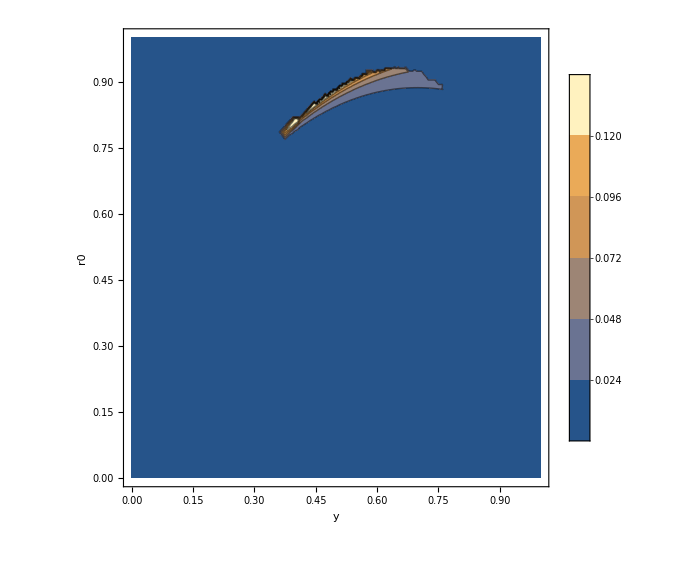

```mathematica
Clear["Global`*"]
SetDirectory["/Users/laurenmcquillan/Documents/Nathan/GitHub/grba_int/cuba-4.2"];
(*SetDirectory["/Users/frankmbp/GitHub/grba_int/cuba-4.2"];*)
Install["Vegas"];
Install["Cuhre"];
Install["Divonne"];
Install["Suave"];

(*Constant definitions*)
TORAD=π/180.;
THV=6.0*TORAD;
KAPPA=0.0;
SIGMA=2.0;
K=0.0;
P=2.2;
GA=1.0;
BG=(1.0-P)/2.0;
GK=(4.0-K)*GA^2;
CK=(4.0-K)*(5.0-K)^((K-5.0)/(4.0-K));
TANTHV=Tan[THV];
TANTHVSQ=TANTHV^2;
SIN2THV=Sin[2.0*THV];
COSTHV=Cos[THV];
SINTHV=Sin[THV];
CHIEXP=(7.0*K-23.0+BG*(13.0+K))/(6.0*(4.0-K));
YEXP=0.5*(BG*(4.0-K)+4.0-3.0*K);

(*Function definitions*)
thp[phi_,r_]:=(r*√(COSTHV^2-0.25*SIN2THV^2*Cos[phi]^2))/(1+0.5*r*SIN2THV*Cos[phi]);
energy[phi_,r_]:=2^(-(thp[phi,r]/SIGMA)^(2*KAPPA));
gamma[phi_,r_]:=GA*√energy[phi,r];
chi[x_,y_]:=(y-CK*x^2)/y^(5-K);
x[phi_,r_,y_]:=√(r^2+y^2*TANTHVSQ+2.0*y*TANTHV*Cos[phi]*r);
x0[r0_,y_]:=r0+y*TANTHV;
yMin[x_?NumericQ]:=y/.FindRoot[y-y^(5-K)-CK*x^2,{y,0.1}];
yMax[x_?NumericQ]:=y/.FindRoot[y-y^(5-K)-CK*x^2,{y,0.9}];
rPrime[y_,r0_,phi_]:=-√(r0^2+2*r0*y*TANTHV+y^2*TANTHVSQ*Cos[phi]^2)-y*TANTHV*Cos[phi];
func[y_,r0_,phi_]:=(rPrime[y,r0,phi]/r0)^2;
r0Max[y_]:=√((y-y^(5-K))/CK)-y*TANTHV;
IG[y_,chi_]:=y^YEXP*chi^CHIEXP*((7.0-2.0*K)*chi*y^(4.0-K)+1.0)^(BG-2.0);
integrandRP[phi_,r_,y_]:=If[chi[x[phi,r,y],y]≥1,(r+y*TANTHV*Cos[phi])*IG[y,chi[x[phi,r,y],y]],0.0];
integrandRP2[phi_,r_]:=NIntegrate[integrandRP[phi,r,y],{y,yMin[r],yMax[r]}];
integrandR0[y_,r0_,phi_]:=If[chi[x0[r0,y],y]≥1,(r0+y*TANTHV)*func[y,r0,phi]*gamma[phi,rPrime[y,r0,phi]]^(4*(1-BG))*IG[y,chi[x0[r0,y],y]],0.0];
integrandR0Alt[y_,r0_,phi_]:=If[0<r0≤r0Max[y],(r0+y*TANTHV)*func[y,r0,phi]*IG[y,chi[x0[r0,y],y]],0.0];(**gamma[phi,rPrime[y,r0,phi]]^(4*(1-BG))*)
integrandR02[y_,r0_]:=If[0<r0≤r0Max[y],NIntegrate[integrandR0[y,r0,phi],{phi,0,2*π},AccuracyGoal->9],0];
integrandR0y[y_]:=NIntegrate[integrandR0[y,r0,phi],{r0,0,r0Max[y]},{phi,0,2*π},AccuracyGoal->7];

(*Plotting*)
(*DensityPlot3D[integrandRP[phi,r,y],{phi,0,2*π},{r,0,1},{y,0,1},PlotLegends->Automatic,AxesLabel->Automatic]*)
ContourPlot[integrandR02[y,r0],{y,0,1},{r0,0,1},ImageSize->Large,PlotRange->All,Contours->5,PlotLegends->Automatic,AxesLabel->Automatic]
(*Plot[integrandR0y[y],{y,0,1}]*)
(*Cuhre[2.0*π*√((y-chi*y^(5-K))/CK)*IG[y,chi],{chi,1,Infinity},{y,chi^(1/(K-4)),1},AccuracyGoal->5,Verbose->0];*)
(*AbsoluteTiming[Cuhre[2.0*π*x*IG[y,chi[x,y]],{x,0,1},{y,yMin[x],yMax[x]},AccuracyGoal->5,Verbose->0]]*)
(*Cuhre[integrand[phi,r,y],{phi,0,2*π},{r,0,1},{y,yMin[r],yMax[r]},AccuracyGoal->5,Verbose->0]//AbsoluteTiming
Suave[integrand[phi,r,y],{phi,0,2*π},{r,0,1},{y,yMin[r],yMax[r]},AccuracyGoal->5,Verbose->0]//AbsoluteTiming*)
(*Cuhre[integrandR0Alt[y,r0,phi],{y,0,1},{r0,0,r0Max[y]},{phi,0,2*π},AccuracyGoal->5,Verbose->0,MaxPoints->100000]//AbsoluteTiming
Suave[integrandR0Alt[y,r0,phi],{y,0,1},{r0,0,r0Max[y]},{phi,0,2*π},AccuracyGoal->5,Verbose->0,MaxPoints->100000]//AbsoluteTiming*)
```